## Hong-Yi Wang

## Optical lattice band gap (problem 7.1)

α=V/E_R, E_R=ℏ^2 k^2/2m

```mathematica
CO=10;(*cutoff*)
gap:=Function[{α},
M=SparseArray[{{j_,j_}:>(2(j-CO)-1)^2+α/2,Band[{1,2}]->α/4,Band[{2,1}]->α/4},{2CO,2CO}];
eigs=Sort@Eigenvalues[M];
eigs[[2]]-eigs[[1]]
]
```

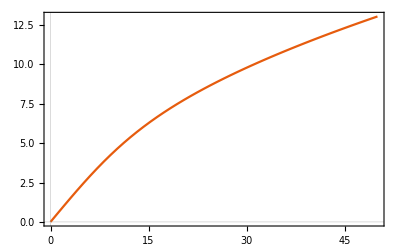

```mathematica
Plot[gap[α],{α,0,50},PlotRange->Full,PlotTheme->"Scientific"]
```

## Dirac point merging (problem 7.5)

```mathematica
a1={0,√3};
a2={3,-√3}/2;
a3={-3,-√3}/2;
J3=1.;
h[k_]:=-(1+Exp[-ⅈ k.a3]+Exp[ⅈ k.a2])-J3((*Exp[ⅈ k.a1]+*)Exp[ⅈ k.(a2-a3)](*+Exp[-ⅈ k.a1]*));
Plot3D[Abs@h@{kx,ky},{kx,-3.4,3.4},{ky,-3.4,3.4},PlotTheme->"Scientific",ColorFunction->"TemperatureMap",MaxRecursion->6]
```

-Graphics3D-

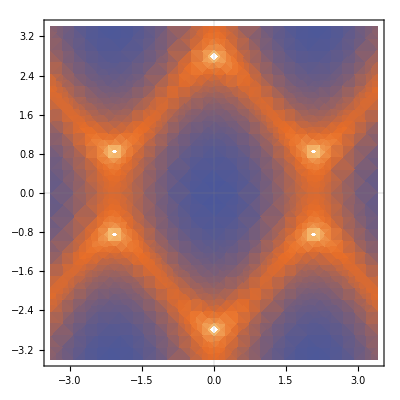

```mathematica
J3=0.5;
DensityPlot[-Log@Abs@h@{kx,ky},{kx,-3.4,3.4},{ky,-3.4,3.4},PlotTheme->"Scientific"]
```

```mathematica
Cross[a1]
```

{-√3,0}

```mathematica
Γ={0,2π 2/(3 √3)};
Γ//N
```

{0.,2.4184}

## Chern number of Haldane model (problem 7.6)

```mathematica
B[k_]:={-(1+Cos[k.a3]+Cos[k.a2]),Sin[k.a3]-Sin[k.a2],M+2Sin@ϕ(Sin[k.a1]+Sin[k.a2]+Sin[k.a3])}//Normalize;
Ω=Assuming[{kx∈Reals,ky∈Reals,M∈Reals,ϕ∈Reals},Cross[D[B@{kx,ky}, kx],D[B@{kx,ky}, ky]].B@{kx,ky}/2//FullSimplify]
```

(3 √3 (M Sin[√3 ky]+(3-2 Cos[3 kx]+4 Cos[(3 kx)/2] Cos[(√3 ky)/2] (-2+Cos[√3 ky])+2 Cos[√3 ky]+Cos[2 √3 ky]) Sin[ϕ]))/(4 ((1+2 Cos[(3 kx)/2] Cos[(√3 ky)/2])^2+4 Cos[(√3 ky)/2]^2 Sin[(3 kx)/2]^2+(M+2 (-2 Cos[(3 kx)/2] Sin[(√3 ky)/2]+Sin[√3 ky]) Sin[ϕ])^2)^(3/2))

```mathematica
Chern[M_,ϕ_]:=NIntegrate[1/(2π)(3 √3 (M Sin[√3 ky]+(3-2 Cos[3 kx]+4 Cos[(3 kx)/2] Cos[(√3 ky)/2] (-2+Cos[√3 ky])+2 Cos[√3 ky]+Cos[2 √3 ky]) Sin[ϕ]))/(4 ((1+2 Cos[(3 kx)/2] Cos[(√3 ky)/2])^2+4 Cos[(√3 ky)/2]^2 Sin[(3 kx)/2]^2+(M+2 (-2 Cos[(3 kx)/2] Sin[(√3 ky)/2]+Sin[√3 ky]) Sin[ϕ])^2)^(3/2)),{kx,0,(4π)/3},{ky,0,(2π)/(√3)},AccuracyGoal->5];
```

```mathematica
Cs=ParallelTable[Chern[M,ϕ]//Quiet,{M,-6,6,.05},{ϕ,-π,π,π/50}];
```

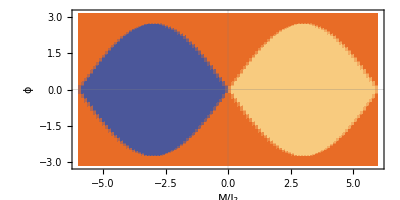

```mathematica
ListDensityPlot[Cs,DataRange->{{-6.,6.},{-π,π}},FrameLabel->{"M/J_2","ϕ"},PlotTheme->"Scientific",AspectRatio->1/2]
```

## Fermi Surface (problem 8.5)

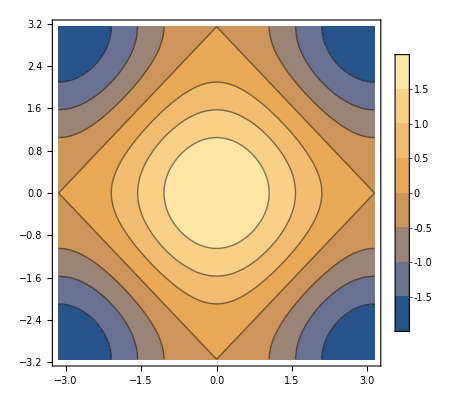

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,-π,π},{y,-π,π},PlotTheme->"Detailed"]
```